# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["/Users/pcs/Desktop/Entropy/QMB_offline.wl"];
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
(*Compute the Page value using the digamma function*)
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
```

# Analysis

```mathematica
L=6;
g=1.0;
J=1.0;
h=0.01;
H=IsingNNOpenHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
ipreigenvec=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

```mathematica
La=L/2;
Lb=L-La;
diagentro=ParallelTable[Chop[sdiag[L,La,Lb,i]],{i,eigenvec}];
```

```mathematica
tlist=Table[10^i,{i,-2,5,0.002}];
tlist//Length
```

3501

```mathematica
Clear[productstate2];
productstate2=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,productstate2},DistributedContexts->Full];
sorted=SortBy[Transpose[{productstate2,iprs}],Last];
productstate=sorted[[1;;10]][[All,1]];
svntproduct=Table[ParallelTable[{t,svn[L,La,Lb,i,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,productstate}];
newenergies=Table[Chop[Conjugate[i].H.i],{i,productstate}];
newiprs=Table[Total[Abs[i]^4],{i,productstate}];
longmean=Table[Mean[svntproduct[[i]][[All,2]][[-500;;-1]]],{i,Length[productstate]}];
```

```mathematica
Export["states_10RPS_open_L_"<>ToString[L]<>"_La_half_J_1_g_"<>ToString[N[g]]<>"_h_"ToString[0.01]".m",productstate];
Export["data_10RPS_open_L_"<>ToString[L]<>"_La_half_J_1_g_"<>ToString[N[g]]<>"_h_"ToString[0.01]".m",svntproduct];
```

Export::chtype: First argument 0.01 .m states_10RPS_open_L_6_La_half_J_1_g_1._h_ is not a valid file specification.

Export::chtype: First argument 0.01 data_10RPS_open_L_6_La_half_J_1_g_1._h_ .m is not a valid file specification.

```mathematica
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Black],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Single RPS",Black,30]},PlotStyle->{Directive[Gray,Opacity[0.4]]}];
svnplotmean=ListLogLinearPlot[Mean[svntproduct],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Mean RPS",Black,30]},PlotStyle->{Directive[Red,Opacity[1.0],PointSize[0.003]]}];
plot1=Show[{svnplots,svnplotmean,pageplot},PlotRange->{All,{0.05,Log[2^La]}}];
pageplot=Plot[pageEntropy[La,Lb],{x,Min[eigenval],Max[eigenval]},PlotStyle->Directive[Dashed,Black],PlotLegends->{Style["Page value = "<>ToString[N[pageEntropy[La,Lb]]],Black,30]}];
plot3=Show[ListPlot[{Transpose[{eigenval,diagentro}],Transpose[{newenergies,longmean}]},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["h = "<>ToString[h]<>" , L = "<>ToString[L]<>", La = "<>ToString[La]<>", E_i",35,Black],FrameLabel->{Style["E",35,Black],Style["Svn",35,Black]},FrameStyle->Directive[Black,20],ImageSize->1000,PlotStyle->{Directive[Gray,Opacity[1]],Directive[Red,Opacity[1]]},PlotLegends->{Style["E_i",Black,30],Style["Svn RPS",Black,30]}],pageplot];
Export["svn_10RPS_open_L_"<>ToString[L]<>"_La_half_J_1_g_"<>ToString[N[g]]<>"_h_"ToString[N[h]]".png",plot1,ImageResolution->300];
Export["scatter_10RPS_open_L_"<>ToString[L]<>"_La_half_J_1_g_"<>ToString[N[g]]<>"_h_"ToString[N[h]]".png",plot3,ImageResolution->300];
```

Export::chtype: First argument 0.01 .png svn_10RPS_open_L_6_La_half_J_1_g_1._h_ is not a valid file specification.

Export::chtype: First argument 0.01 .png scatter_10RPS_open_L_6_La_half_J_1_g_1._h_ is not a valid file specification.

# Random phase evolution

```mathematica
neweigenval=RandomReal[{-1,1},2^L];
```

```mathematica
svntproductfake=Table[ParallelTable[{t,svn[L,La,Lb,i,neweigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,productstate}];
```

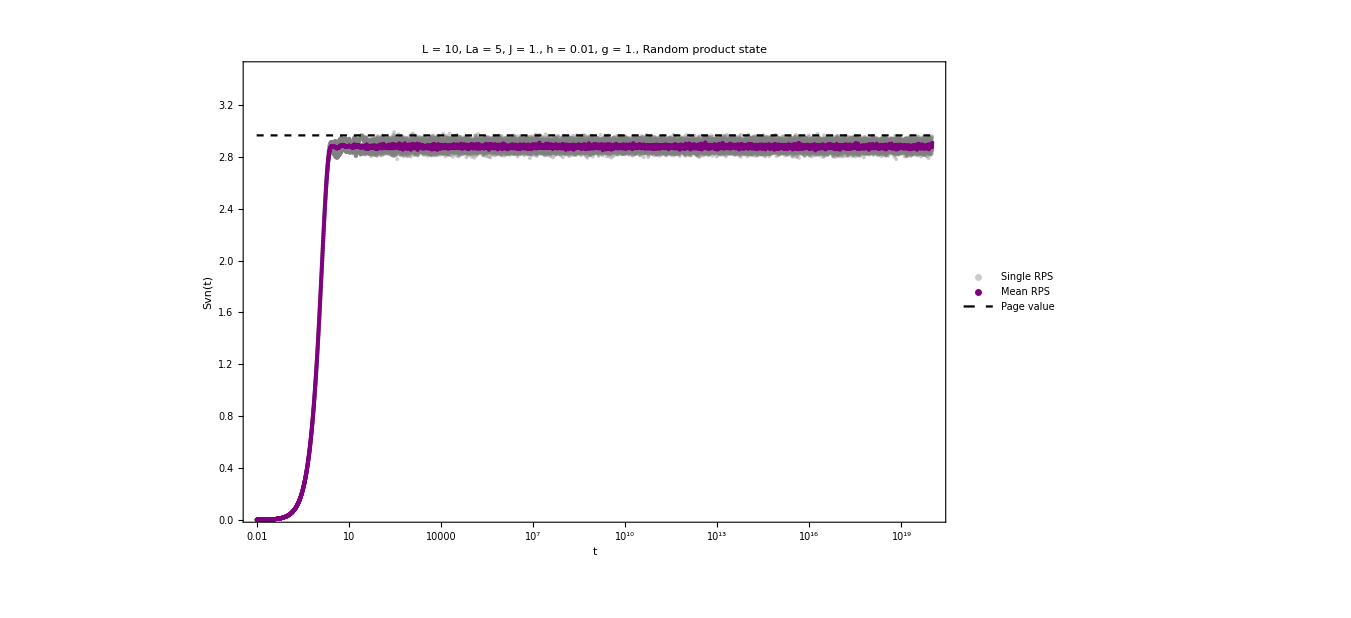

```mathematica
longmean=Table[Mean[svntproductfake[[i]][[All,2]][[-500;;-1]]],{i,Length[productstate]}];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Black],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproductfake,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Single RPS",Black,30]},PlotStyle->{Directive[Gray,Opacity[0.4]]}];
svnplotmean=ListLogLinearPlot[Mean[svntproductfake],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Mean RPS",Black,30]},PlotStyle->{Directive[Purple,Opacity[1.0],PointSize[0.003]]}];
plot4=Show[{svnplots,svnplotmean,pageplot},PlotRange->{All,{0.05,Log[2^La]}}]
```

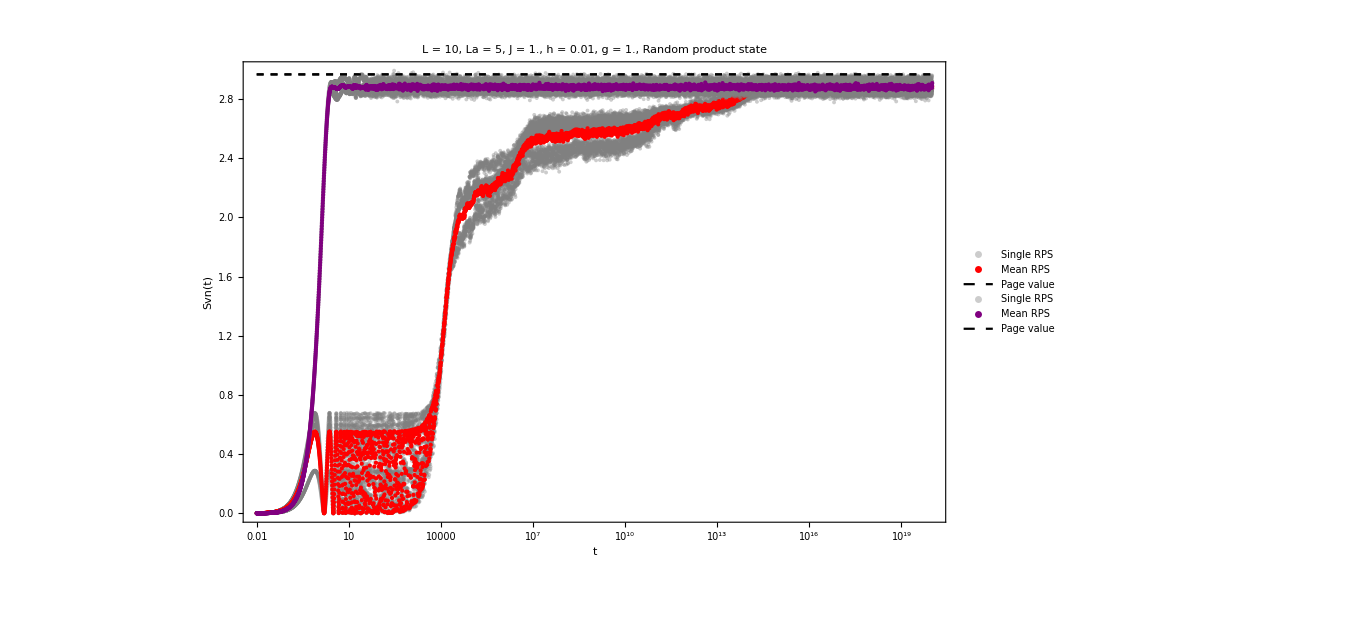

```mathematica
Show[{plot1,plot4},PlotRange->All]
```

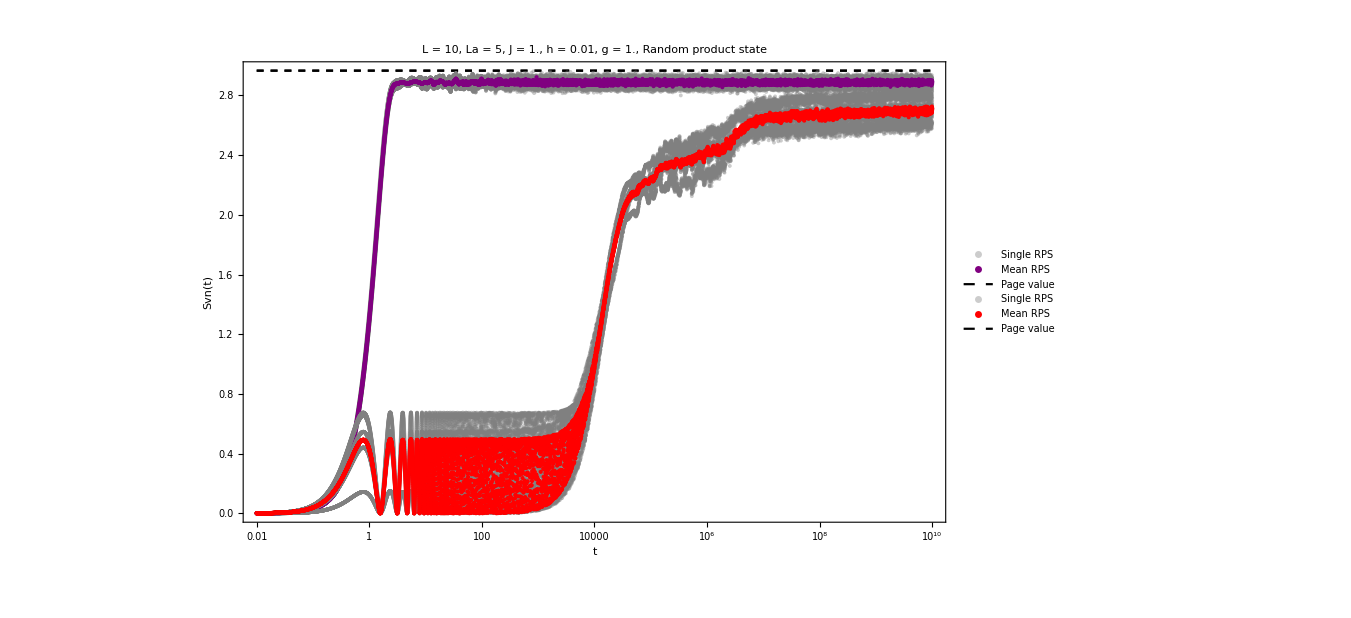

```mathematica
Show[{plot4,plot1},PlotRange->All]
```